```mathematica
(* From http://mathematica.stackexchange.com/a/13122 *)
ortlinfit[data_?MatrixQ,errs_?MatrixQ]:=Module[{n=Length[data],c,ct,dk,dm,k,m,p,s,st,ul,vl,w,wt,xm,ym},(*yes,I know I could have used FindFit[] for this...*){ct,st,k}=Flatten[MapAt[Normalize[{1,#}]&,NArgMin[Norm[Function[{x,y},y-m x-k]@@@data],{m,k}],1]];
(*find orthogonal regression coefficients*){c,s,p}=FindArgMin[{Total[(data.{-s,c}-p)^2/((errs^2).{s^2,c^2})],c^2+s^2==1},{{c,ct},{s,st},{p,k/ct}}];
(*slope and intercept*){m,k}={s,p}/c;
wt=1/errs^2;w=(Times@@@wt)/(wt.{1,m^2});
{xm,ym}=w.data/Total[w];
ul=data[[All,1]]-xm;vl=data[[All,2]]-ym;
(*uncertainties in slope and intercept*)dm=w.(m ul-vl)^2/w.ul^2/(n-2);
dk=dm (w.data[[All,1]]^2/Total[w]);
{Function[x,Evaluate[{m,k}.{x,1}]],Sqrt[{dm,dk}]}]/;Dimensions[data]===Dimensions[errs]
```

```mathematica
xV = Pi r^2 dldP P dP + V dP;
yV = power dt - Pi r^2 dldP P dP;
xP = P dV;
yP = power dt;
ΔxV = Norm[
Grad[xV,{r, dldP, P, V, dP, dV, power, dt}] {Δr, ΔdldP, ΔP, ΔV, ΔdP, 0, Δpower, Δdt}
];
ΔyV = Norm[
Grad[yV,{r, dldP, P, V, dP, dV, power, dt}] {Δr, ΔdldP, ΔP, ΔV, ΔdP, 0, Δpower, Δdt}
];
ΔxP = Norm[
Grad[xP,{r, dldP, P, V, dP, dV, power, dt}] {Δr, ΔdldP, ΔP, ΔV, 0, ΔdV, Δpower, Δdt}
];
ΔyP = Norm[
Grad[yP,{r, dldP, P, V, dP, dV, power, dt}] {Δr, ΔdldP, ΔP, ΔV, 0, ΔdV, Δpower, Δdt}
];
```

```mathematica
R = Quantity["MolarGasConstant"];
current = Quantity[630, "Milliamperes"];
voltage = Quantity[4.44, "Volts"];
power = UnitConvert[current voltage, "Watts"];
P = Quantity[1035, "Millibars"];
V = Quantity[10, "Liters"];
r = Quantity[3.8 / 2, "Millimeters"];
dldP = Quantity[65, "Millimeters"/"Millibars"];
```

```mathematica
Δcurrent = Quantity[10, "Milliamperes"];
Δvoltage = Quantity[0.01, "Volts"];
Δpower = UnitConvert[
Norm[{current Δvoltage, Δcurrent voltage}],
"Watts"
];
ΔP = Quantity[0.25, "Millibars"];
ΔV = Quantity[0.25, "Liters"];
Δr = Quantity[0.05/2, "Millimeters"];
ΔdldP = Quantity[0.5, "Millimeters"/"Millibars"];
ΔdP = Quantity[0.05, "Millibars"];
ΔdV = Quantity[0.25, "Centimeters"^3];
Δdt = Quantity[0.5, "Milliseconds"];
```

{Function[x$,-0.223995+4.23396 x$],{0.470261,0.490454}}

0.96129

-0.223995+4.23396 x

0.697718+5.19525 x

-1.14571+3.27267 x

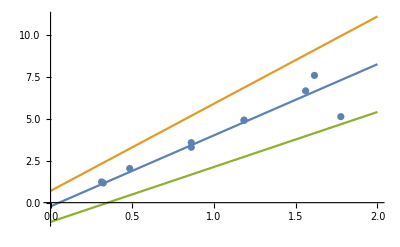

```mathematica
rawData = Import["~/mnt/lab1/constant-volume.tsv"][[2;;All]];
data = QuantityMagnitude@UnitConvert[({xV, yV} /. {
dP ->  Quantity[#[[1]], "Millibars"],
dt ->  Quantity[#[[2]], "Milliseconds"]
} &)/@rawData];errors = QuantityMagnitude@UnitConvert[({ΔxV, ΔyV} /. {
dP ->  Quantity[#[[1]], "Millibars"],
dt ->  Quantity[#[[2]], "Milliseconds"]
} &)/@rawData];
Export["~/mnt/lab1/constant-volume-transformed.tsv", Join[
{{"x", "y", "Dx", "Dy"}},Transpose@Join[Transpose[data], Transpose[errors]]
]];
{fit, errs} = ortlinfit[data, errors/1.96]
1.96 errs[[2]]
fit = fit[x]
fita = Simplify[fit + 1.96(errs[[1]] + errs[[2]] x)]
fitb = Simplify[fit - 1.96(errs[[1]] + errs[[2]] x)]
Show[Plot[{fit, fita, fitb}, {x, 0, 2}], ListPlot[data]]
```

{Function[x$,-0.0847765+4.05986 x$],{0.254188,0.15897}}

0.311581

-0.0847765+4.05986 x

0.413432+4.37144 x

-0.582985+3.74828 x

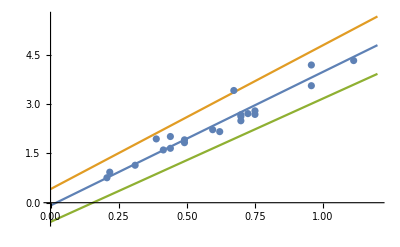

```mathematica
rawData = Import["~/mnt/lab1/constant-pressure.tsv"][[2;;All]];
data = QuantityMagnitude@UnitConvert[({xP, yP} /. {
dV ->  Quantity[#[[1]], "Centimeters"^3],
dt ->  Quantity[#[[2]], "Milliseconds"]
} &)/@rawData];
errors = QuantityMagnitude@UnitConvert[({ΔxP, ΔyP} /. {
dV ->  Quantity[#[[1]], "Centimeters"^3],
dt ->  Quantity[#[[2]], "Milliseconds"]
} &)/@rawData];
Export["~/mnt/lab1/constant-pressure-transformed.tsv", Join[
{{"x", "y", "Dx", "Dy"}},Transpose@Join[Transpose[data], Transpose[errors]]
]];
{fit, errs} = ortlinfit[data, errors/1.96]
1.96 errs[[2]]
fit = fit[x]
fita = Simplify[fit + 1.96(errs[[1]] + errs[[2]] x)]
fitb = Simplify[fit - 1.96(errs[[1]] + errs[[2]] x)]
Show[Plot[{fit, fita, fitb}, {x, 0, 1.2}], ListPlot[data]]
```